```mathematica
Sx=(h/2)*PauliMatrix[1];
```

```mathematica
Sy=(h/2)*PauliMatrix[2];
```

```mathematica
Sz=(h/2)*PauliMatrix[3];
```

```mathematica
Id=IdentityMatrix[2];
```

```mathematica
S1S2=KroneckerProduct[Sx,Sx]+KroneckerProduct[Sy,Sy]+KroneckerProduct[Sz,Sz];
```

```mathematica
SZ1=KroneckerProduct[Sz,Id];
```

```mathematica
H=-J*S1S2-B*SZ1;
```

```mathematica
Eigensystem[H]//FullSimplify
```

{{-1/4 h (2 B+h J),-1/4 h (-2 B+h J),1/4 h (h J-2 √(B^2+h^2 J^2)),1/4 h (h J+2 √(B^2+h^2 J^2))},{{1,0,0,0},{0,0,0,1},{0,(B+√(B^2+h^2 J^2))/(h J),1,0},{0,(B-√(B^2+h^2 J^2))/(h J),1,0}}}

```mathematica
A={{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
Eigensystem[A]
```

{{0,0},{{0,1},{0,0}}}

```mathematica
B={{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
A.B-B.A
```

{{0,0},{0,0}}

```mathematica
ψ1=Sqrt[2/L]*Sin[Pi*x/L];
```

```mathematica
ψ2=Sqrt[2/L]*Sin[2*Pi*x/L];
```

```mathematica
N[Integrate[(a*ψ1+b*ψ2)^2,{x,0,L/2}]/.{a->1/Sqrt[2],b->1/Sqrt[2]}]
```

0.924413

```mathematica
Integrate[(a*ψ1*Exp[I*Pi^2*t/(2*L^2)]+b*ψ2*Exp[4*I*Pi^2*t/(2*L^2)])*(a*ψ1*Exp[-I*Pi^2*t/(2*L^2)]+b*ψ2*Exp[-4*I*Pi^2*t/(2*L^2)]),{x,L/2,L}]
```

1/2 (a^2+b^2)-(8 a b Cos[(3 π^2 t)/(2 L^2)])/(3 π)

```mathematica
u0=(ω/Pi)^(1/4)*Exp[-ω*x^2/2];
```

```mathematica
u1=Exp[-a*x^2];
```

```mathematica
Integrate[u0*x^4*u0,{x,-Infinity,Infinity}]
```

ConditionalExpression[3/(4 ω^2), Re[ω]>0]

```mathematica
Integrate[u1*(-(1/2)*D[u1,{x,2}]+(1/2)*ω^2*x^2*u1),{x,-Infinity,Infinity}]/Integrate[u1^2,{x,-Infinity,Infinity}]//FullSimplify
```

ConditionalExpression[(4 a^2+ω^2)/(8 a), Re[a]>0]

```mathematica
(4 a^2+ω^2)/(8 a)/.{a->ω/2}
```

ω/2

```mathematica
(6 √2 λ)/(8 a^2)
```

(3 λ)/(2 √2 a^2)

```mathematica
D[(4 a^2+ω^2)/(8 a),a]//FullSimplify
```

1/2-ω^2/(8 a^2)

```mathematica
Solve[1/2-ω^2/(8 a^2)==0,a]//FullSimplify
```

{{a→-ω/2},{a→ω/2}}

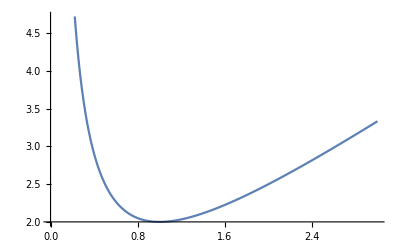

```mathematica
Plot[(x^2+1)/x,{x,0,3}]
```